# Program for the computation of the heat kernel coefficients

Gonzalo Sancho Garrido

First, we define the coefficients  and  that appear on the paper, and are necessary to compute certain .

```mathematica
b[m_,α_,β_]:=Sum[(-1)^(m-j+1)2^(m-2j)Gamma[m-j]Sin[α]^(m-2j)(Cos[β]-Cos[α])^j/(Gamma[j+1]Gamma[m-2j+1](Cos[α]+Cos[β])^(m-j)),{j,0,Floor[m/2]}]
```

```mathematica
c[m_,α_,β_]:=-Cot[α]^m/m
```

Next, we define this function that returns 1 if , and 0 if it doesn’t.  can be parametrized by  and , as it’s indicated in formula (1.5) of the paper, but for our purposes we do not need to use all of the components of , just .

```mathematica
testM[α_,β_,n1_]:=If[-1<=n1<=1,If[0<=α<=Pi,If[-Pi/2<=β<=Pi/2,If[0<=α+β<=Pi,If[0<=α-β<=Pi,1,0],0],0],0],0]
```

Now, we create a function that calculates the determinant of  , which will be useful to find out whether our matrix  belongs in  or not.

```mathematica
detDU[α_,β_,n1_,L_]:=L(Cos[α] -Cos[β])-2(Sin[α]+n1 Sin[β])
```

Similarly to testM, we can define a function that returns 1 if  belongs to the Von Neumann-Krein extension, and 0 if it doesn’t.

```mathematica
testVNK[α_,β_,n1_,L_]:=If[n1==1,If[-Pi/2<=α<=0,If[0<=β<=Pi/2,If[α==-β,If[β == ArcTan[2/L],1,0],0],0],0],0]
```

The formula for the  coefficients will be different depending of the values of  and , so we need to define a function that computes  for each of the different cases.

Formulas (3.32)-(3.33)

```mathematica
a1[n_,α_,β_,L_]:=Which[n<0,0,n==0,L/Sqrt[4Pi],n==1/2,1/2,IntegerQ[n],-4^(n-1)Factorial[n-1]b[2n-1,α,β]/(Factorial[2n-2]Sqrt[Pi]),IntegerQ[2n],-b[2n-1,α,β]/Factorial[n-3/2],True,0]
```

Formulas (3.42)-(3.43)

```mathematica
a2[n_,α_,β_,L_]:=Which[n<0,0,n==0,L/Sqrt[4Pi],n==1/2,0,IntegerQ[n],-4^(n-1)Factorial[n-1]c[2n-1,α,β]/(Factorial[2n-2]Sqrt[Pi]),IntegerQ[2n],-c[2n-1,α,β]/Factorial[n-3/2],True,0]
```

Formulas (3.44)

```mathematica
a3[n_,α_,β_,L_]:=Which[n==0,L/(2Sqrt@Pi),n==1/2,-1/2,True,0]
```

Formulas (3.52)-(3.54)

```mathematica
a4[n_,α_,β_,L_]:=Which[n<0,0,n==0,L/Sqrt[4Pi],n==1/2,1/2,IntegerQ[n],-4^(n-1)Factorial[n-1]Tan[α]^(2n-1)/(Factorial[2n-1]Sqrt[Pi]),IntegerQ[2n],1/2 Tan[α]^(2n-1)/Factorial[n-1/2],True,0]
```

Formula (3.58)

```mathematica
a5[n_,α_,β_,L_]:=If[n==0,L/(2Sqrt@Pi),0]
```

Formulas (3.61)-(3.62)

```mathematica
a6[n_,α_,β_,L_]:=Which[n==0,L/Sqrt[4Pi],n==1/2,1/2,IntegerQ[n],Factorial[n-1](4/L)^(2n-1)/(Factorial[2n-1]2Sqrt[Pi]),IntegerQ[2n],1/2 (2/L)^(2n-1)/Factorial[n-1/2],True,0]
```

With all of this, we can define a function that gives us the coefficient  depending on the values of the parameters, checking which formula should be applied depending on their value. It is valid for both  and .  The parameter  can be left as an undefined variable in the first case, but

```mathematica
a[n_,α_,β_,n1_,L_]:=Which[testM[α,β,n1]==1,If[Refine[detDU[α,β,n1,L]==0,L>0],If[α==Pi/2,a5[n,α,β,L],a4[n,α,β,L]],If[Abs[β]==Pi-α,If[α==Pi,a3[n,α,β,L],a2[n,α,β,L]],a1[n,α,β,L]]],testVNK[α,β,n1,L]==1,a6[n,α,β,L],True,"The values of the parameters are not valid."]
```

We can define coefficients for higher dimensions, divided by the (hyper)surface of the plates.

```mathematica
aD[n_,α_,β_,n1_,L_,D_Integer]:=(2Sqrt[Pi])^(1-D)a[n,α,β,n1,L]
```

It is also possible to give the coefficients for a massive field. Usually, the massless case is the most interesting one, but having the massive coefficients might prove to be useful in some cases.

```mathematica
am[n_,α_,β_,n1_,L_,m_]:=Sum[a[n-j,α,β,n1,L](-m^2)^j/Factorial@j,{j,0,n}]
```

We now show all the coefficients up to  for some boundary conditions

Periodic boundary conditions:

```mathematica
Table[a[n,Pi/2,-Pi/2,1,L],{n,0,5,1/2}]
```

{L/(2 √π),0,0,0,0,0,0,0,0,0,0}

Dirichlet boundary conditions:

```mathematica
Table[a[n,Pi,0,1,L],{n,0,5,1/2}]
```

{L/(2 √π),-1/2,0,0,0,0,0,0,0,0,0}

Neumann boundary conditions:

```mathematica
Table[a[n,0,0,1,L],{n,0,5,1/2}]
```

{L/(2 √π),1/2,0,0,0,0,0,0,0,0,0}

Robin boundary conditions, with :

```mathematica
Table[a[n,Pi/2,0,1,L],{n,0,5,1/2}]
```

{L/(2 √π),1/2,-2/(√π),1,-4/(3 √π),1/2,-8/(15 √π),1/6,-16/(105 √π),1/24,-32/(945 √π)}

This is a plot of all the heat kernel coefficients up to a maximum  for adjustable values of  and . One has to be careful, because if the values are chosen such that , the plot will not display anything.  can also be manipulated, but it only affects  in this case.

```mathematica
Manipulate[DiscretePlot[a[m,α,β,1,L],{m,0,n,1/2}],{n,0,20,1/2},{α,0,Pi},{β,-Pi/2,Pi/2},{L,0,20}]
```

In this plot,  is fixed to 0, and one can only vary , which means general Robin boundary conditions. Here, all the values of  are valid.

```mathematica
Manipulate[DiscretePlot[a[m,α,0,1,L],{m,0,n,1/2}],{n,0,20,1/2},{α,0,Pi},{L,0,20}]
```

This one if for the case , that is,  (we choose  always).

```mathematica
Manipulate[DiscretePlot[a[m,α,-α,1,L],{m,0,n,1/2}],{n,0,20,1/2},{α,0,Pi/2},{L,0,20}]
```

This one is for the case , which is only possible for .

```mathematica
Manipulate[DiscretePlot[a[m,α,Pi-α,1,L],{m,0,n,1/2}],{n,0,20,1/2},{α,Pi/2,Pi},{L,0,20}]
```

Finally, this last plot is for  that belong to the Von Neumann Krein extension. In this case, all the coefficients (save for ) do depend on .

```mathematica
Manipulate[DiscretePlot[a[m,-ArcTan[2/L],ArcTan[2/L],1,L],{m,0,n,1/2}],{n,0,20,1/2},{L,0.01,5}]
```

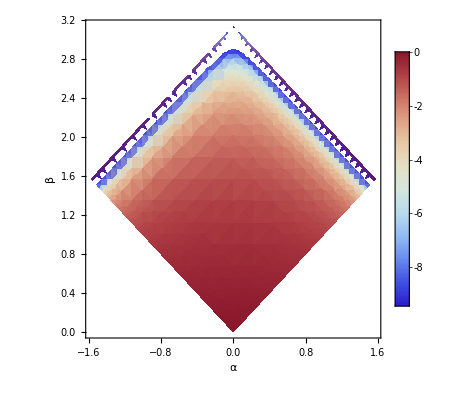

```mathematica
DensityPlot[a[1,α,β,1,L],{β,-Pi/2,Pi/2},{α,0,Pi},PlotLegends->Automatic,FrameLabel->{HoldForm[α],HoldForm[β]},ColorFunction->"ThermometerColors",Exclusions->testM[α,β,1]==0,MeshFunctions->{#3&},Mesh->{{0}},MeshStyle->Dashed]
```

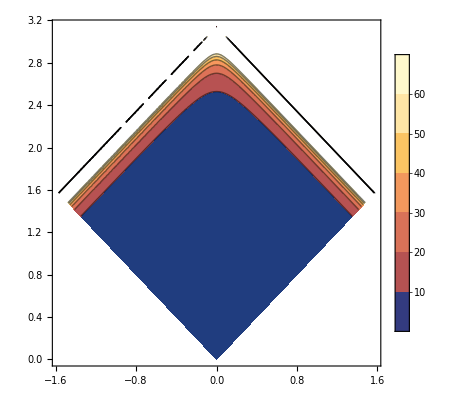

```mathematica
ContourPlot[a[3/2,α,β,1,L],{β,-Pi/2,Pi/2},{α,0,Pi},PlotLegends->Automatic]
```

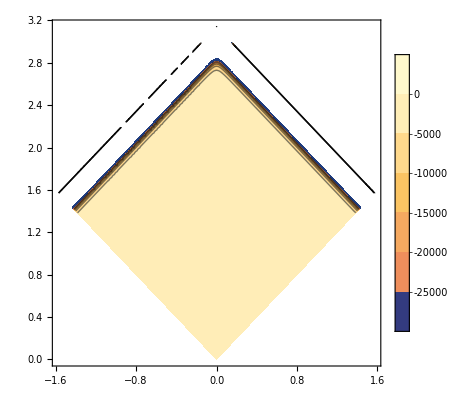

```mathematica
ContourPlot[a[4,α,β,1,L],{β,-Pi/2,Pi/2},{α,0,Pi},PlotLegends->Automatic]
```

```mathematica
aD[0,Pi/2,0,1,L,3]
```

L/(8 π^(3/2))

```mathematica
aD[1,Pi/2,0,1,L,3/2]
```

-(√2)/π^(3/4)

```mathematica
Format[title1,TraditionalForm]:=""
```

```mathematica
Format[title2,TraditionalForm]:=""
```

```mathematica
Format[title3,TraditionalForm]:=""
```

```mathematica
Format[title4,TraditionalForm]:=""
```

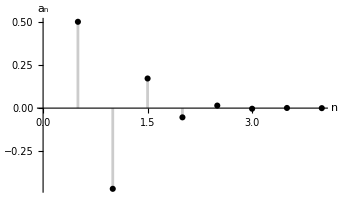

```mathematica
DiscretePlot[a[m,Pi/4,0,1,L],{m,0,4,1/2},AxesLabel->{HoldForm[],HoldForm[]},PlotRange->Full,PlotStyle->Black,LabelStyle->{GrayLevel[0]},PlotLabel->title1]
```

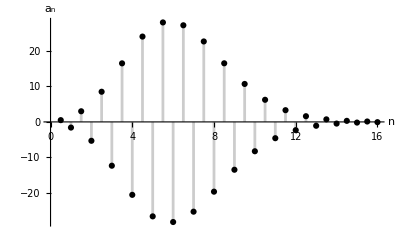

```mathematica
DiscretePlot[a[m,Pi/2,Pi/4,1,L],{m,0,16,1/2},{AxesLabel->{HoldForm[],HoldForm[]},PlotRange->Full,PlotStyle->Black,LabelStyle->{GrayLevel[0]}},PlotLabel->title2]
```

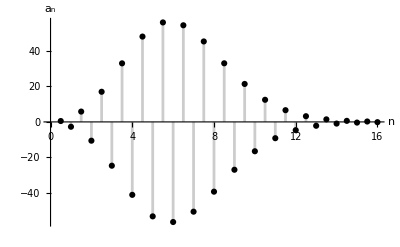

```mathematica
DiscretePlot[a[m,3Pi/4,0,1,L],{m,0,16,1/2},AxesLabel->{HoldForm[],HoldForm[]},PlotRange->Full,PlotStyle->Black,LabelStyle->{GrayLevel[0]},PlotLabel->title3]
```

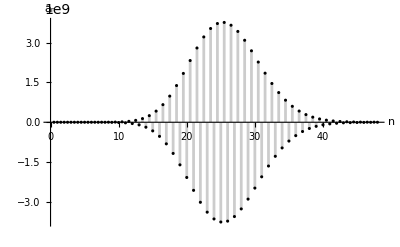

```mathematica
DiscretePlot[a[m,3Pi/4,Pi/8,1,L],{m,0,48,1/2},AxesLabel->{HoldForm[],HoldForm[]},PlotRange->Full,PlotStyle->Black,LabelStyle->{GrayLevel[0]},PlotLabel->title4]
```

```mathematica
a[21,5Pi/6,0,1,L]//N
```

-26478.

```mathematica
b[49,3Pi/4,0]//N
```

8.93514×10^18

```mathematica
4^35*35!b[70,5Pi/6,0]/70!//N
```

3.09313×10^9

```mathematica
a1[35,5Pi/6,0,L]//N
```

-4.38533×10^9

```mathematica
Table[am[n,0,0,1,1,m],{n,0,5,1/2}]
```

{1/(2 √π),1/2,-m^2/(2 √π),-m^2/2,m^4/(4 √π),m^4/4,-m^6/(12 √π),-m^6/12,m^8/(48 √π),m^8/48,-m^10/(240 √π)}

```mathematica
Grid[Transpose[Table[{Subscript[Style["a",Italic, FontFamily->"Times"],ToString[n,InputForm]],a[n,Pi,0,1,L]},{n,0,5,1/2}]],Frame->All,ItemSize->All]
```

a_0 | a_(1/2) | a_1 | a_(3/2) | a_2 | a_(5/2) | a_3 | a_(7/2) | a_4 | a_(9/2) | a_5
L/(2 √π) | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Grid[Transpose[Table[{Subscript[Style["a",Italic, FontFamily->"Times"],ToString[n,InputForm]],a[n,Pi/2,0,1,L]},{n,0,5,1/2}]],Frame->All,ItemSize->All]
```

a_0 | a_(1/2) | a_1 | a_(3/2) | a_2 | a_(5/2) | a_3 | a_(7/2) | a_4 | a_(9/2) | a_5
L/(2 √π) | 1/2 | -2/(√π) | 1 | -4/(3 √π) | 1/2 | -8/(15 √π) | 1/6 | -16/(105 √π) | 1/24 | -32/(945 √π)